```mathematica
(*https://www.notion.so/methematica13-1-ca7e708575964f8a8feb6a7a44986bfd*)
```

```mathematica
V[t_]:=A(1+k*∑_(n=0)^(+2000) (4M)/((2n+1)*Pi)*Sin[(2n+1)*2Pi*1000*t])*Cos[2Pi*100000*t];
M=5;
A=2;
k=0.1;
```

```mathematica
V[t];
```

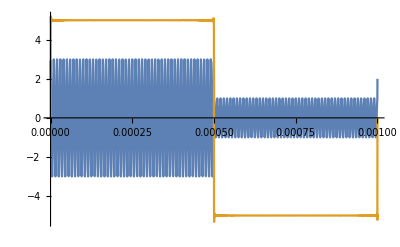

```mathematica
Plot[{V[t],∑_(n=0)^(+2000) (4M)/((2n+1)*Pi)*Sin[(2n+1)*2Pi*1000*t]},{t,0,1/1000}]
```

```mathematica
MaxValue[V[t],t]
```

2.99989

```mathematica
MinValue[V[t],t]
```

-3.00016